## Module - vary Mp

This module studies how varying only the projectile mass affects our trebuchet.

#### Mod

```mathematica
v45[mpr_]:=
Module[{Lcw,Ls,Lb,theta0,phi0,thetashot,Mp=mpr,Mcw ,Mb,Mbase,Msy,g,Lt,V,theta,t,phi,xp,yp,xcw,ycw,Ib,xpd,ypd,xcwd,ycwd,T,L,sol,x,tmax,thetaDer,xder,vxpro,vypro,xpos,ypos,thetat,tshot,vshot,EL},

EL[q_]:=D[L,q[t]]-D[D[L,q'[t]],t]==0;
Mb=0.045;
theta0 = Pi/4;
phi0 = 0;
Lt=.99;
Lcw=.115;
Ls=.35;
Lb = Lt-Ls;
thetashot=-Pi/4;
Mcw = 0.162;
Mbase = 0.485;
Msy = Mbase+Mb+Mcw+Mp;
g =9.81;

V= -Mp*Lb* Sin[theta[t]]*g + (Ls*Sin[theta[t]]-Lcw*Cos[phi[t]])*g*Mcw - 1/2 *Sin[theta[t]]*Mb*g*(Lb-Ls);

xp =- Lb *Cos[theta[t]]+x[t];
yp = - Lb*Sin[theta[t]];
xcw = Ls *Cos[theta[t]]+x[t]+Lcw *Sin[phi[t]];
ycw = Ls *Sin[theta[t] ]-Lcw *Cos[phi[t]];
Ib =Mb*1/3 ((Lb^3+Ls^3)/(Lb+Ls));
xpd=D[xp,t];
ypd=D[yp,t];
xcwd=D[xcw,t];
ycwd=D[ycw,t];
T=1/2*Mp* (xpd^2+ypd^2)+1/2 *Mcw*(xcwd^2+ycwd^2)+Msy*1/2*x'[t]^2+1/2 *Ib*theta'[t]^2;

L = T-V;

sol = First[NDSolve[{EL[theta],EL[phi],EL[x],
x[0]==0,
theta[0]==theta0,
phi[0]== phi0,
x'[0]==0,
theta'[0]==0,
phi'[0]==0},{x,theta,phi},{t,0,tmax=10}]];

thetaDer[t_]=D[theta[t]/.sol,t];
xder[t_]=D[x[t]/.sol,t];
vxpro[t_] :=Lb *Sin[theta[t]/.sol]*thetaDer[t]+xder[t];
vypro[t_]:=-Lb*Cos[theta[t]/.sol]*thetaDer[t];
xpos[t_] :=-Lb Cos[theta[t]/.sol]+x[t]/.sol;
ypos[t_]:=-Lb Sin[theta[t]/.sol];
thetat[t_]:= theta[t]/.sol;
tshot=Solve[thetat[t]== thetashot,t][[1,1,2]];
vshot=Sqrt[vxpro[tshot]^2+vypro[tshot]^2]
]
```

Here we set the minimum and maximum values of the projectile.

```mathematica
mprmin=0.0005;
mprmax=0.02;
```

```mathematica
vDat=Monitor[Table[ {mpr,v45[mpr]},{mpr, mprmin,mprmax,0.0001}],mpr];
```

```mathematica
peaks=FindPeaks[Flatten[vDat,1]];
```

For our trebuchet we were interested in the peaks.

```mathematica
peaksEdit=peaks[[All,1]]
```

{2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254,256,258,260,262,264,266,268,270,272,274,276,278,280,282,284,286,288,290,292,294,296,298,300,302,304,306,308,310,312,314,316,318,320,322,324,326,328,330,332,334,336,338,340,342,344,346,348,350,352,354,356,358,360,362,364,366,368,370,372,374,376,378,380,382,384,386,388,390,392}

```mathematica
data=Flatten[vDat,1][[peaksEdit]];
```

```mathematica
data[[All,1]]+data[[All,2]];
```

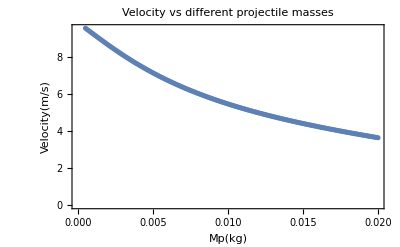

```mathematica
Countorv=ListPlot[vDat, Frame-> True, PlotLabel->"Velocity vs different projectile masses", FrameLabel->{"Mp(kg)","Velocity(m/s)"}]
```